## test for F(theta1,theta 2)

need to solve possion function

note bmu = β μ and bJ= β J

(∂^2 ψ)/(∂theta1^2)+(∂^2 ψ)/(∂theta2^2)=(-bmu(Cos[theta1]+Cos[theta2]+QX))Exp[bJ Cos[theta1-theta2]+bmu Ε (Cos[theta1]+Cos[theta2])];

```mathematica
Qx=Qx0+Qx1 Ε;
Qx0=0;
F[theta1_,theta2_]:=(-bmu(Cos[theta1]+Cos[theta2])+Qx)Exp[bJ Cos[theta1-theta2]+bmu Ε (Cos[theta1]+Cos[theta2])]
F0=Normal[Series[F[theta1,theta2],{Ε,0,0}]]//Simplify
F1=(Normal[Series[F[theta1,theta2],{Ε,0,1}]]-F0)//Simplify
```

-bmu ⅇ^(bJ Cos[theta1-theta2]) (Cos[theta1]+Cos[theta2])

ⅇ^(bJ Cos[theta1-theta2]) Ε (Qx1-bmu^2 Cos[theta1]^2-2 bmu^2 Cos[theta1] Cos[theta2]-bmu^2 Cos[theta2]^2)

```mathematica
Qy=Qy0+Qy1 Ε;
Qy0=0;
F[theta1_,theta2_]:=(-bmu(Sin[theta1]+Sin[theta2])+Qy)Exp[bJ Cos[theta1-theta2]+bmu Ε ( Sin[theta1]+Sin[theta2])]
F0=Normal[Series[F[theta1,theta2],{Ε,0,0}]]//Simplify
F1=(Normal[Series[F[theta1,theta2],{Ε,0,1}]]-F0)//Simplify
```

-bmu ⅇ^(bJ Cos[theta1-theta2]) (Sin[theta1]+Sin[theta2])

ⅇ^(bJ Cos[theta1-theta2]) Ε (Qy1-bmu^2 Sin[theta1]^2-2 bmu^2 Sin[theta1] Sin[theta2]-bmu^2 Sin[theta2]^2)

add one more expansion

```mathematica
Exp[bJ Cos[theta1-theta2]]=∑_(j=0)^N (bJ)^j/j! Cos[theta1-theta2]^j ;
```

Set::write: Tag Exp in Exp[bJ Cos[theta1-theta2]] is Protected.

then we have

## Set up

### Expressions

#### vE

```mathematica
Qy0=0;
Qy1=bmu^2+(bmu^2 BesselI[1,bJ])/BesselI[0,bJ];
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qy0-bmu(Sin[theta1]+Sin[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qy1-bmu^2(Sin[theta1]+Sin[theta2])^2+Qy0 bmu(Sin[theta1]+Sin[theta2]))
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

```mathematica
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
```

```mathematica
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
```

```mathematica
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
```

```mathematica
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
```

```mathematica
pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

#### vEE

```mathematica
H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

small question here, I1CCH integrate along theta1?

```mathematica
F1s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1sch[n,j,2Pi]+1/(2n)I1ssh[n,j,2Pi]
F1c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1cch[n,j,2Pi]+1/(2n)I1csh[n,j,2Pi]
E1s[n_,j_]:=F1s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1ssh[n,j,2Pi]
E1c[n_,j_]:=F1c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1csh[n,j,2Pi]
```

```mathematica
A1c[0,j_,theta1_]:=Integrate[H1[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A1s[0,j_,theta1_]:=0
A1s[n_,j_,theta1_]:=E1s[n,j]Sinh[n theta1]+F1s[n,j]Cosh[n theta1]+1/n I1ssh[n,j,theta1]
A1c[n_,j_,theta1_]:=E1c[n,j]Sinh[n theta1]+F1c[n,j]Cosh[n theta1]+1/n I1csh[n,j,theta1]
dA1c[0,j_,theta1_]:=Integrate[H1[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA1s[0,j_,theta1_]:=0
dA1s[n_,j_,theta1_]:=n E1s[n,j]Cosh[n theta1]+n F1s[n,j]Sinh[n theta1]+I1sch[n,j,theta1]
dA1c[n_,j_,theta1_]:=n E1c[n,j]Cosh[n theta1]+n F1c[n,j]Sinh[n theta1]+I1cch[n,j,theta1]
```

```mathematica
pv11[bJx_,bmux_,xi_,xj_]:=Sum[dA1s[n,j,theta1]Sin[n theta2]+dA1c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv21[bJx_,bmux_,xi_,xj_]:=Sum[n A1s[n,j,theta1]Cos[n theta2]-n A1c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

```mathematica
(*pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]*)
```

### Export and import(export part commented)

#### zero order

Hns

```mathematica
(*Export["~/Dropbox/Export/Y/H0y.xls",Table[{j,H0[0,j,theta1]},{j,0,10}]];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/H0cy.xls",Table[{n,j,H0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/H0sy.xls",Table[{n,j,H0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
H0y=Flatten[Import["~/Dropbox/Export/Y/H0y.xls"],1];
Table[H0[0,j_,xi_]:=ToExpression[H0y[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H0cy=Flatten[Import["~/Dropbox/Export/Y/H0cy.xls"],1];
Table[H0c[n_,j_,xi_]:=ToExpression[H0cy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H0sy=Flatten[Import["~/Dropbox/Export/Y/H0sy.xls"],1];
Table[H0s[n_,j_,xi_]:=ToExpression[H0sy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

Ins

```mathematica
(*Timing[Export["~/Dropbox/Export/Y/I0cchy.xls",Table[{n,j,I0cch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify]];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/I0schy.xls",Table[{n,j,I0sch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/I0cshy.xls",Table[{n,j,I0csh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/I0sshy.xls",Table[{n,j,I0ssh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I0cchy=Flatten[Import["~/Dropbox/Export/Y/I0cchy.xls"],1];
Table[I0cch[n_,j_,xi_]:=ToExpression[I0cchy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0schy=Flatten[Import["~/Dropbox/Export/Y/I0schy.xls"],1];
Table[I0sch[n_,j_,xi_]:=ToExpression[I0schy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0cshy=Flatten[Import["~/Dropbox/Export/Y/I0cshy.xls"],1];
Table[I0csh[n_,j_,xi_]:=ToExpression[I0cshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0sshy=Flatten[Import["~/Dropbox/Export/Y/I0sshy.xls"],1];
Table[I0ssh[n_,j_,xi_]:=ToExpression[I0sshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Export["~/Dropbox/Export/Y/F0sy.xls",Table[{n,j,F0s[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/F0cy.xls",Table[{n,j,F0c[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/E0sy.xls",Table[{n,j,E0s[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/E0cy.xls",Table[{n,j,E0c[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
F0sy=Flatten[Import["~/Dropbox/Export/Y/F0sy.xls"],1];
Table[F0s[n_,j_]:=ToExpression[F0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F0cy=Flatten[Import["~/Dropbox/Export/Y/F0cy.xls"],1];
Table[F0c[n_,j_]:=ToExpression[F0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0sy=Flatten[Import["~/Dropbox/Export/Y/E0sy.xls"],1];
Table[E0s[n_,j_]:=ToExpression[E0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0cy=Flatten[Import["~/Dropbox/Export/Y/E0cy.xls"],1];
Table[E0c[n_,j_]:=ToExpression[E0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*
Export["~/Dropbox/Export/Y/A0cy0.xls",Table[{j,A0c[0,j,theta1]},{j,0,10}]//Simplify];
Export["~/Dropbox/Export/Y/A0cy.xls",Table[{n,j,A0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/A0sy.xls",Table[{n,j,A0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/dA0cy0.xls",Table[{j,dA0c[0,j,theta1]},{j,0,10}]//Simplify];
Export["~/Dropbox/Export/Y/dA0cy.xls",Table[{n,j,dA0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];
*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/dA0sy.xls",Table[{n,j,dA0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
A0cy0=Flatten[Import["~/Dropbox/Export/Y/A0cy0.xls"],1]
```

{{0.,bmu*Sin[theta1]},{1.,(bJ*bmu*Sin[theta1])/2},{2.,(bJ^2*bmu*Sin[theta1])/4},{3.,(bJ^3*bmu*Sin[theta1])/16},{4.,(bJ^4*bmu*Sin[theta1])/64},{5.,(bJ^5*bmu*Sin[theta1])/384},{6.,(bJ^6*bmu*Sin[theta1])/2304},{7.,(bJ^7*bmu*Sin[theta1])/18432},{8.,(bJ^8*bmu*Sin[theta1])/147456},{9.,(bJ^9*bmu*Sin[theta1])/1474560},{10.,(bJ^10*bmu*Sin[theta1])/14745600}}

```mathematica
Table[A0c[0,j,theta1],{j,9,9}]//Simplify
```

{(bJ^9 bmu Sin[theta1])/1474560}

```mathematica
A0cy0=Flatten[Import["~/Dropbox/Export/Y/A0cy0.xls"],1];
A0cy=Flatten[Import["~/Dropbox/Export/Y/A0cy.xls"],1];
Table[A0c[0,j_,theta1_]:=ToExpression[A0cy0[[j+1,2]]],{j,0,10}];  
Table[A0c[n_,j_,theta1_]:=ToExpression[A0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A0sy=Flatten[Import["~/Dropbox/Export/Y/A0sy.xls"],1];
A0s[0,j,theta1]:=0;
Table[A0s[n_,j_,theta1_]:=ToExpression[A0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0cy0=Flatten[Import["~/Dropbox/Export/Y/dA0cy0.xls"],1];
dA0cy=Flatten[Import["~/Dropbox/Export/Y/dA0cy.xls"],1];
Table[dA0c[0,j_,theta1_]:=ToExpression[dA0cy0[[j+1,2]]],{j,0,10}];
Table[dA0c[n_,j_,theta1_]:=ToExpression[dA0cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0sy=Flatten[Import["~/Dropbox/Export/Y/dA0sy.xls"],1];
dA0s[0,j,theta1]:=0;
Table[dA0s[n_,j_,theta1_]:=ToExpression[dA0sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

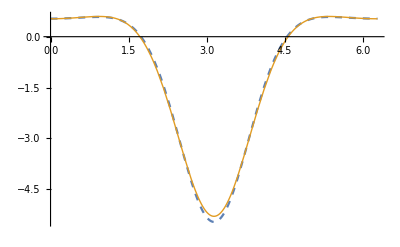

```mathematica
nmax=2;jmax=6;
myt2=Pi;
Plot[{pv10[1,1,x,myt2]Exp[Cos[x-myt2]],pv20[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

#### first order

```mathematica
(*Export["~/Dropbox/Export/Y/H1y.xls",Table[{j,H1[0,j,theta1]},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/H1cy.xls",Table[{n,j,H1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/H1sy.xls",Table[{n,j,H1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
H1y=Flatten[Import["~/Dropbox/Export/Y/H1y.xls"],1];
(*c2=RandomInteger[{5,10}]
H1[0,c2,theta1]
H1[0,c2,theta1]-ToExpression[H1y[[c2+1,2]]]//Simplify*)
```

```mathematica
Table[A1c[0,j_,xi_]:=ToExpression[H1y[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H1cy=Flatten[Import["~/Dropbox/Export/Y/H1cy.xls"],1];
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
H1c[c1,c2,theta1]
H1c[c1,c2,theta1]-ToExpression[H1cy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1c[n_,j_,xi_]:=ToExpression[H1cy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H1sy=Flatten[Import["~/Dropbox/Export/Y/H1sy.xls"],1];
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
H1s[c1,c2,theta1]//Simplify
H1s[c1,c2,theta1]-ToExpression[H1sy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1s[n_,j_,xi_]:=ToExpression[H1sy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Timing[Export["~/Dropbox/Export/Y/I1cchy.xls",Table[{n,j,I1cch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify]]*)
```

{60.6893,~/Dropbox/Export/Y/I1cchy.xls}

```mathematica
(*Export["~/Dropbox/Export/Y/I1schy.xls",Table[{n,j,I1sch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/I1cshy.xls",Table[{n,j,I1csh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/I1sshy.xls",Table[{n,j,I1ssh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
I1cchy=Flatten[Import["~/Dropbox/Export/Y/I1cchy.xls"],1];
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1cch[c1,c2,theta1]
%-ToExpression[I1cchy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1cch[n_,j_,xi_]:=ToExpression[I1cchy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1schy=Flatten[Import["~/Dropbox/Export/Y/I1schy.xls"],1];
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1sch[c1,c2,theta1]
%-ToExpression[I1schy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1sch[n_,j_,xi_]:=ToExpression[I1schy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1cshy=Flatten[Import["~/Dropbox/Export/Y/I1cshy.xls"],1];
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1csh[c1,c2,theta1]
%-ToExpression[I1cshy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1csh[n_,j_,xi_]:=ToExpression[I1cshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1sshy=Flatten[Import["~/Dropbox/Export/Y/I1sshy.xls"],1];
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1ssh[c1,c2,theta1]
%-ToExpression[I1sshy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1ssh[n_,j_,xi_]:=ToExpression[I1sshy[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
(*Export["~/Dropbox/Export/Y/F1sy.xls",Table[{n,j,F1s[n,j]},{n,1,5},{j,0,10}]//Simplify];
Export["~/Dropbox/Export/Y/F1cy.xls",Table[{n,j,F1c[n,j]},{n,1,5},{j,0,10}]//Simplify];
Export["~/Dropbox/Export/Y/E1sy.xls",Table[{n,j,E1s[n,j]},{n,1,5},{j,0,10}]//Simplify];
Export["~/Dropbox/Export/Y/E1cy.xls",Table[{n,j,E1c[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
F1sy=Flatten[Import["~/Dropbox/Export/Y/F1sy.xls"],1];
Table[F1s[n_,j_]:=ToExpression[F1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F1cy=Flatten[Import["~/Dropbox/Export/Y/F1cy.xls"],1];
Table[F1c[n_,j_]:=ToExpression[F1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1sy=Flatten[Import["~/Dropbox/Export/Y/E1sy.xls"],1];
Table[E1s[n_,j_]:=ToExpression[E1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1cy=Flatten[Import["~/Dropbox/Export/Y/E1cy.xls"],1];
Table[E1c[n_,j_]:=ToExpression[E1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
(*Export["~/Dropbox/Export/Y/A1cy0.xls",Table[{j,A1c[0,j,theta1]},{j,0,10}]//Simplify];
Export["~/Dropbox/Export/Y/A1cy.xls",Table[{n,j,A1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/A1sy.xls",Table[{n,j,A1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/dA1cy0.xls",Table[{j,dA1c[0,j,theta1]},{j,0,10}]//Simplify];
Export["~/Dropbox/Export/Y/dA1cy.xls",Table[{n,j,dA1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Export/Y/dA1sy.xls",Table[{n,j,dA1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
A1cy0=Flatten[Import["~/Dropbox/Export/Y/A1cy0.xls"],1];
A1cy=Flatten[Import["~/Dropbox/Export/Y/A1cy.xls"],1];
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
A1c[c1,c2,theta1]//Simplify
%-ToExpression[A1cy[[11*(c1-1)+c2+1,3]]]//Simplify
A1c[0,c2,theta1]-ToExpression[A1cy0[[c2+1,2]]]//Simplify*)
```

```mathematica
Table[A1c[0,j_,theta1_]:=ToExpression[A1cy0[[j+1,2]]],{j,0,10}];
Table[A1c[n_,j_,theta1_]:=ToExpression[A1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A1sy=Flatten[Import["~/Dropbox/Export/Y/A1sy.xls"],1];
(*A1s[0,j,theta1]:=0;
c1=RandomInteger[{1,5}];
c2=RandomInteger[{0,10}];
A1s[c1,c2,theta1]
%-ToExpression[A1sy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[A1s[n_,j_,theta1_]:=ToExpression[A1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1cy0=Flatten[Import["~/Dropbox/Export/Y/dA1cy0.xls"],1];
dA1cy=Flatten[Import["~/Dropbox/Export/Y/dA1cy.xls"],1];
```

```mathematica
Table[dA1c[0,j_,theta1_]:=ToExpression[dA1cy0[[j+1,2]]],{j,0,10}];
Table[dA1c[n_,j_,theta1_]:=ToExpression[dA1cy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1sy=Flatten[Import["~/Dropbox/Export/Y/dA1sy.xls"],1];
dA1s[0,j,theta1]:=0;
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1s[c1,c2,theta1]-ToExpression[dA1sy[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1s[n_,j_,theta1_]:=ToExpression[dA1sy[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

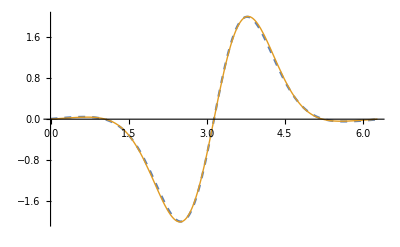

```mathematica
nmax=jmax=3;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

## Pv10 and pv20

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

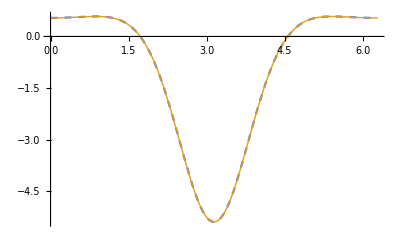

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv10[1,1,x,myt2]Exp[Cos[x-myt2]],pv20[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

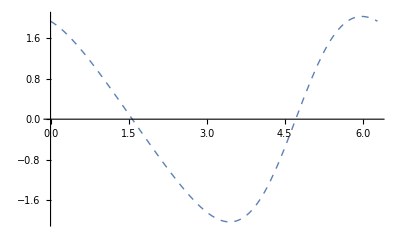

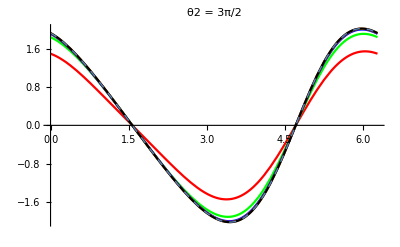

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv10[1,1,x,myt2],{x,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=2;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=3;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=4;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=5;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
plot[nmax+1]=Plot[pv20[1,1,myt2,x],{x,0,2Pi},PlotStyle->{Dashed,Thick}]
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```

## P11 and P21

```mathematica
Qy0=0;(*for coupling J is zero*)
Qy1=bmu^2+(bmu^2  BesselI[1,bJ])/BesselI[0,bJ]//N
```

bmu^2+(bmu^2 BesselI[1.,bJ])/BesselI[0.,bJ]

```mathematica
n=1;j=1
dA1s[n,j,theta1]Cos[n theta2]
```

1

-(bJ bmu^2 Cos[theta1] (20 BesselI[1,J β]+BesselI[0,J β] (-13+6 Cos[2 theta1])) Cos[theta2])/(40 BesselI[0,J β])

```mathematica
n=1;j=1
dA1c[n,j,theta1]Cos[n theta2]
```

1

(bJ bmu^2 (20 BesselI[1,J β]+BesselI[0,J β] (13+6 Cos[2 theta1])) Cos[theta2] Sin[theta1])/(40 BesselI[0,J β])

```mathematica
Sum[dA1s[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,1},{j,0,1}]
```

bmux^2 Cos[xi] Sin[xj]-(bJx bmux^2 Cos[xi] (20 BesselI[1,J β]+BesselI[0,J β] (-13+6 Cos[2 xi])) Sin[xj])/(40 BesselI[0,J β])

```mathematica
Sum[dA1c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,1},{j,0,1}]
```

```mathematica
0.+(bJx bmux^2 (20 BesselI[1,J β]+BesselI[0,J β] (13+6 Cos[2 xi])) Cos[xj] Sin[xi])/(40 BesselI[0,J β])+1/2 bJx bmux^2 (π-xi+Cos[xi] Sin[xi])+(bmux^2 (-2 (π-xi) BesselI[1,J β]+BesselI[0,J β] Cos[xi] Sin[xi]))/(2 BesselJ βI[0,J β])
```

```mathematica
n=j=1;
dA1s[n,j,theta1]Sin[n theta2]+dA1c[n,j,theta1]Cos[n theta2]
```

(bJ bmu^2 (20 BesselI[1,J β]+BesselI[0,J β] (13+6 Cos[2 theta1])) Cos[theta2] Sin[theta1])/(40 BesselI[0,J β])-(bJ bmu^2 Cos[theta1] (20 BesselI[1,J β]+BesselI[0,J β] (-13+6 Cos[2 theta1])) Sin[theta2])/(40 BesselI[0,J β])

```mathematica
nmax=jmax=1;
```

```mathematica
pv11[1,1,xi,xj]
```

0.+((20 BesselI[1,J β]+BesselI[0,J β] (13+6 Cos[2 xi])) Cos[xj] Sin[xi])/(40 BesselI[0,J β])+1/2 (π-xi+Cos[xi] Sin[xi])+(-2 (π-xi) BesselI[1,J β]+BesselI[0,J β] Cos[xi] Sin[xi])/(2 BesselI[0,J β])+Cos[xi] Sin[xj]-(Cos[xi] (20 BesselI[1,J β]+BesselI[0,J β] (-13+6 Cos[2 xi])) Sin[xj])/(40 BesselI[0,J β])

```mathematica
nmax=jmax=1;
v11=pv11[1,1,theta1,theta2]//Simplify
v22=pv21[1,1,theta2,theta1]//Simplify
```

1/(40 BesselI[0,J β])(20 BesselI[1,J β] (-2 π+2 theta1+Sin[theta1-theta2])+BesselI[0,J β] (20 π-20 theta1+20 Sin[2 theta1]-20 Sin[theta1-theta2]+3 Sin[3 theta1-theta2]+30 Sin[theta1+theta2]))

1/40 (10 Cos[theta2] Sin[theta1]+Sin[theta1-3 theta2]+(20 BesselI[1,J β] Sin[theta1-theta2])/BesselI[0,J β]+50 Cos[theta1] Sin[theta2])

```mathematica
myt2=Pi
pv11[1,1,x,myt2]Exp[Cos[x-myt2]]//Simplify
Plot[%,{x,0,2Pi}]
```

π

```mathematica
Plot[(ⅇ^(-Cos[x]) (-20 BesselI[1,J β] (2 π-2 x+Sin[x])+BesselI[0,J β] (20 π-20 x-10 Sin[x]+20 Sin[2 x]-3 Sin[3 x])))/(40 BesselI[0,J β]),{x,0,2Pi}]
```

-Graphics-

```mathematica
nmax=jmax=1;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

-Graphics-

```mathematica
nmax=jmax=2;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

Part::partw: Part 3 of {0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"} does not exist.

ToExpression::notstrbox: {{0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"}, {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"}, « 7 », {9., "(bJ^9*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/1474560"}, {10., "(bJ^10*bmu^2*(-24*(Pi - theta1)*BesselI[1, J*\[Beta]] + 11*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(353894400*BesselI[0, J*\[Beta]])"}} ⟦ 1, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"} does not exist.

ToExpression::notstrbox: {{0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"}, {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"}, « 7 », {9., "(bJ^9*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/1474560"}, {10., "(bJ^10*bmu^2*(-24*(Pi - theta1)*BesselI[1, J*\[Beta]] + 11*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(353894400*BesselI[0, J*\[Beta]])"}} ⟦ 2, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of {2., "(bJ^2*bmu^2*(-8*(Pi - theta1)*BesselI[1, J*\[Beta]] + 3*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(32*BesselI[0, J*\[Beta]])"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ToExpression::notstrbox: {{0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"}, {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"}, « 7 », {9., "(bJ^9*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/1474560"}, {10., "(bJ^10*bmu^2*(-24*(Pi - theta1)*BesselI[1, J*\[Beta]] + 11*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(353894400*BesselI[0, J*\[Beta]])"}} ⟦ 3, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

-Graphics-

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

Part::partw: Part 3 of {0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"} does not exist.

ToExpression::notstrbox: {{0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"}, {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"}, « 7 », {9., "(bJ^9*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/1474560"}, {10., "(bJ^10*bmu^2*(-24*(Pi - theta1)*BesselI[1, J*\[Beta]] + 11*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(353894400*BesselI[0, J*\[Beta]])"}} ⟦ 1, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"} does not exist.

ToExpression::notstrbox: {{0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"}, {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"}, « 7 », {9., "(bJ^9*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/1474560"}, {10., "(bJ^10*bmu^2*(-24*(Pi - theta1)*BesselI[1, J*\[Beta]] + 11*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(353894400*BesselI[0, J*\[Beta]])"}} ⟦ 2, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of {2., "(bJ^2*bmu^2*(-8*(Pi - theta1)*BesselI[1, J*\[Beta]] + 3*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(32*BesselI[0, J*\[Beta]])"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ToExpression::notstrbox: {{0., "(bmu^2*(-2*(Pi - theta1)*BesselI[1, J*\[Beta]] + BesselI[0, J*\[Beta]]*Cos[theta1]*Sin[theta1]))/(2*BesselI[0, J*\[Beta]])"}, {1., "(bJ*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/2"}, « 7 », {9., "(bJ^9*bmu^2*(Pi - theta1 + Cos[theta1]*Sin[theta1]))/1474560"}, {10., "(bJ^10*bmu^2*(-24*(Pi - theta1)*BesselI[1, J*\[Beta]] + 11*BesselI[0, J*\[Beta]]*Sin[2*theta1]))/(353894400*BesselI[0, J*\[Beta]])"}} ⟦ 3, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

-Graphics-

## test

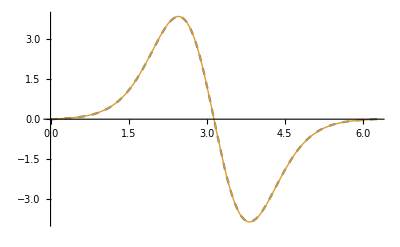

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

```mathematica
nmax=1;jmax=10;
(*pv11[1,1,theta1,theta2]//Simplify
pv21[1,1,theta2,theta1]//Simplify*)
```

```mathematica
1/44236800(-81007533 Sin[theta1]-12402349 Sin[2 theta1-theta2]);
```

```mathematica
1/88473600(-162015066 Sin[theta1]-12402349 Sin[theta1-2 theta2]);
```

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

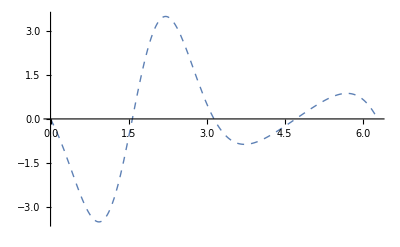

```mathematica
nmax=jmax=4;
myt2=Pi/2;
Plot[{pv11[1,1,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

-Graphics-

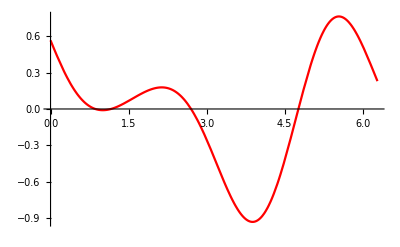

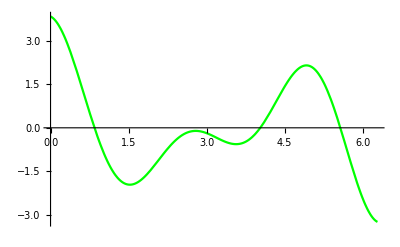

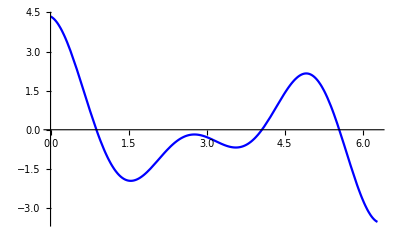

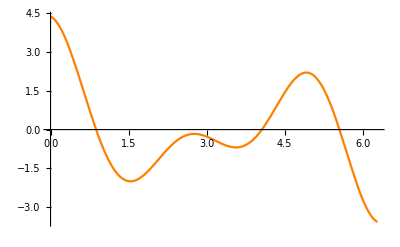

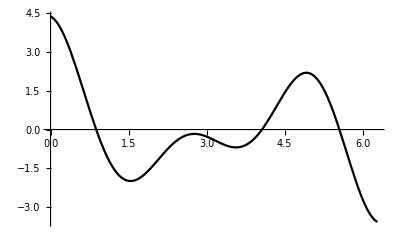

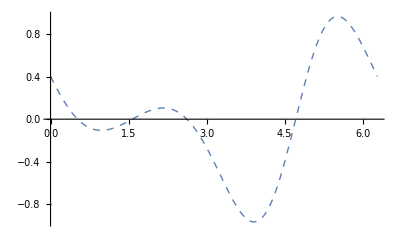

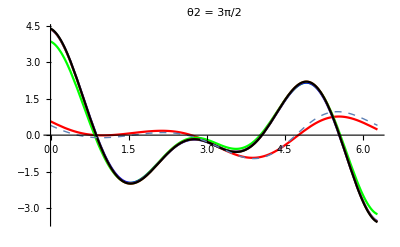

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv11[1,1,x,myt2],{x,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=2;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=3;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=4;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=5;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
plot[nmax+1]=Plot[pv21[1,1,myt2,x],{x,0,2Pi},PlotStyle->{Dashed,Thick}]
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```

### get vEE from p11

```mathematica
nmax=1;jmax=0
pv10[1,1,theta1,theta2]
pv20[1,1,theta1,theta2]
pv11[1,1,theta1,theta2]
pv21[1,1,theta1,theta2]
```

0

0.-Sin[theta1]

Part::partd: Part specification Flatten[$Failed, 1] ⟦ 1, 3 ⟧ is longer than depth of object.

ToExpression::notstrbox: Flatten[$Failed, 1] ⟦ 1, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Failed Cos[theta2]-1. Sin[theta2]

-1.40238+0.44639 theta1-0.5 Cos[theta1] Sin[theta1]-Cos[theta2] Sin[theta1]

0.-Cos[theta1] Sin[theta2]

Note that P11 in Steven’s Sol is

```mathematica
-1/2 bmu^2 (Cos[theta1]+2 Cos[theta2]) Sin[theta1];
```

and we think it’s expression for vEE if we times p, However, it’s not!
P11 is actually A1 in the function below

```mathematica
A=A+A1*Ex+o(Ex^2);
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A + A1\ Ex + Ex^2\ o.

where A = p v^E  and do expansion for p and v^E

```mathematica
p=p0+p1 Ex+ o(Ex^2);
v^E=vE+vEE*Ex+o(Ex^2);
```

Set::write: Tag Power in v^ⅇ is Protected.

so

```mathematica
p v^E  = (p0+p1 Ex+ o(Ex^2))(vE+vEE*Ex+o(Ex^2))=p0 vE + (p0 vEE+p1 vE)Ex + o(Ex^2);
```

Set::write: Tag Times in (Ex^2\ o + p0 + Ex\ p1)\ (Ex^2\ o + vE + Ex\ vEE) is Protected.

Set::write: Tag Times in (Ex^2\ o + p0 + Ex\ p1)\ v^ⅇ is Protected.

we know that

```mathematica
vE=-bmu Sin[theta1];
```

and p0 and p1 would be:

```mathematica
p=ⅇ^(bJ Cos[theta1-theta2]+bmu (Cos[theta1]+Cos[theta2]) Ex)/.bJ->0;
p0=Normal[Series[p,{Ex,0,0}]]
p1=(Normal[Series[p,{Ex,0,1}]]-p0)/Ex
```

1

bmu Cos[theta1]+bmu Cos[theta2]

and again

```mathematica
p11=-1/2 bmu^2 (Cos[theta1]+2 Cos[theta2]) Sin[theta1];
```

then we just need to solve for vEE

```mathematica
vE=-bmu Sin[theta1];
Solve[p0 vEE+p1 vE==p11,vEE]//Simplify
```

{{vEE→1/2 bmu^2 Cos[theta1] Sin[theta1]}}

Horray same with Our analytical result.

```mathematica
(**)
```